The “configurationFile.csv”  was created manually to make a good smoothing of the curves: kernel1 is for the smoothing of epidemic curve (i.e., the curve to which the estimation is made) and the Kernel2-3 is for the smoothing of the first derivative of epidemic curve.

### Getting the data

```mathematica
configFile=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabu/exampleUseLibrary/data/configurationFile.csv"];
configFile[[;;5]]//Grid
```

Country | Code | kernel1 | Kernel2 | Kernel3
Belgium | BE | 18 | 20 | 27
Bolivia | BO | 18 | 18 | 27
Brazil | BR | 50 | 50 | 27
Colombia | CO | 35 | 35 | 27

```mathematica
countries={"Belgium","Bosnia and Herzegovina","Brazil","Colombia","Croatia","Ireland","Italy","Luxembourg","Norway","Republic of Korea","Romania","Spain","The United Kingdom","Türkiye","United States of America"};
```

### Relation 1

When both kernels are the same (kernel1 and Kernel2)

```mathematica
relation1=#[[1]]/#[[2]]&/@configFile[[2;;,{3,4}]]
```

{9/10,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Plots

```mathematica
import[country_]:=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabu/exampleUseLibrary/plots/Waves_"<>country<>"NoN.png"]
import[#]&/@countries
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Relation 2

When both kernels are not the same  (kernel1 and Kernel3)

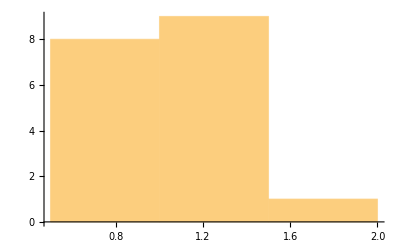

{1.01483,0.310435,0.0963697}

```mathematica
relation2a=#[[1]]/#[[2]]&/@configFile[[2;;,{3,5}]];
Histogram[relation2a]
N[{Mean[#],StandardDeviation[#],Variance[#]}]&@relation2a
```

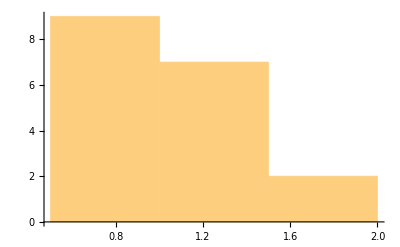

{1.0662,0.294701,0.0868489}

```mathematica
relation2b=#[[2]]/#[[1]]&/@configFile[[2;;,{3,5}]];
Histogram[relation2b]
N[{Mean[#],StandardDeviation[#],Variance[#]}]&@relation2b
```

Plots

```mathematica
import2[country_]:=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabu/exampleUseLibrary/plots/Wavesk3_"<>country<>"NoN.png"]
import2[#]&/@countries
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Differences between both relation1-2

There are very similar but differ in the next countries

```mathematica
-Graphics--Graphics-
(*relation1-kenerl2: Norway:38 UK:20*)
```

```mathematica
-Graphics--Graphics-
(*relation2-kenerl3:Norway:29 UK:29*)
```

### Conclusion

The first and second kernel could be very similar or equal